```mathematica
ListPlot[EntityValue[EntityClass["Country", "Asia"], {"Population", "GDP"}, "EntityAssociation"]]
```

-Graphics-

```mathematica
FeatureExtract[{
{1.4,"A",3.4},{1.5,"A",6.5},{3.2,"B",1.2},{5.4,"B",2.3}
}, "StandardizedVector"]
```

{{A,{-0.908338,0.025278}},{A,{-0.846755,1.59251}},{B,{0.200142,-1.08695}},{B,{1.55495,-0.530838}}}

```mathematica
M= {
{"High","Hot"},
{"Low","Medium"},
{"Low","Mild"},
{"Low","Medium"},
{"Low","Mild"},
{"High","Hot"},
{"Low","Medium"},
{"Low","Mild"},
{"High","Medium"},
{"Low","Hot"}
}
```

{{High,Hot},{Low,Medium},{Low,Mild},{Low,Medium},{Low,Mild},{High,Hot},{Low,Medium},{Low,Mild},{High,Medium},{Low,Hot}}

```mathematica
MatrixForm/@FeatureExtract[M, "IndicatorVector"]
```

{(1.
0.
1.
0.
0.),(0.
1.
0.
1.
0.),(0.
1.
0.
0.
1.),(0.
1.
0.
1.
0.),(0.
1.
0.
0.
1.),(1.
0.
1.
0.
0.),(0.
1.
0.
1.
0.),(0.
1.
0.
0.
1.),(1.
0.
0.
1.
0.),(0.
1.
1.
0.
0.)}

```mathematica
trainDigits={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
testDigits={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
A = AssociationThread[trainDigits, DimensionReduce[trainDigits, 5]]
```

<|-Graphics-→{-0.692231,-6.46778,-5.14908,13.2041,4.97252},-Graphics-→{7.93951,-3.01778,7.86645,-3.01321,-1.32293},-Graphics-→{-10.9833,-16.3836,-9.55104,-10.866,-0.54396},-Graphics-→{1.42164,13.9786,-2.33964,-7.01927,11.7595},-Graphics-→{7.89527,1.00214,-3.21249,5.08864,-5.70942},-Graphics-→{5.93009,-3.00434,-4.21182,5.72812,3.19584},-Graphics-→{7.88658,-2.8815,7.47972,-3.12737,-1.40396},-Graphics-→{7.42544,-2.54643,8.78662,-2.52988,-1.07984},-Graphics-→{-25.7144,4.36401,9.79938,4.2342,-1.0376},-Graphics-→{-1.10855,14.9566,-9.4681,-1.6994,-8.83011}|>

```mathematica
o = L[testDigits]
```

{{-0.675565,-3.10281},{2.12046,-2.3978},{1.89245,16.0024},{-12.1512,-3.6074},{0.835734,-2.68114},{-8.06767,5.1849},{-4.46998,9.28848},{3.93123,-1.87833},{5.98495,-1.09187},{1.92045,-2.38724}}

```mathematica
FeatureSpacePlot[A]
```

```mathematica
FeatureSpacePlot3D[
AssociationThread[
EntityValue[EntityClass["Country", "Europe"],"FlagImage"] , 
DimensionReduce[
EntityValue[EntityClass["Country", "Europe"],"FlagImage"]
]
]
]
```

```mathematica
Show[%60,ViewPoint->{1.3,-2.4,2.}]
```

-Graphics3D-

```mathematica
ExampleData[{"Statistics","FisherIris"},"LongDescription"]
```

The data set consists of 50 samples from each of three species of iris flowers.  Four features were measured from each sample, they are the length and the width of sepal and petal. This data set is often used to demonstrate classification techniques and discriminant analysis.

```mathematica
features = ExampleData[{"Statistics","FisherIris"},"ColumnDescriptions"]
```

{Sepal length in cm.,Sepal width in cm.,Petal length in cm.,Petal width in cm.,Species of iris}

```mathematica
irisData=ExampleData[{"Statistics","FisherIris"}];
```

```mathematica
irisData //Short
```

{{5.1,3.5,1.4,0.2,setosa},«148»,{5.9,3.,5.1,1.8,virginica}}

```mathematica
setosaSamples = Cases[irisData, {___, "setosa"}]
```

{{5.1,3.5,1.4,0.2,setosa},{4.9,3.,1.4,0.2,setosa},{4.7,3.2,1.3,0.2,setosa},{4.6,3.1,1.5,0.2,setosa},{5.,3.6,1.4,0.2,setosa},{5.4,3.9,1.7,0.4,setosa},{4.6,3.4,1.4,0.3,setosa},{5.,3.4,1.5,0.2,setosa},{4.4,2.9,1.4,0.2,setosa},{4.9,3.1,1.5,0.1,setosa},{5.4,3.7,1.5,0.2,setosa},{4.8,3.4,1.6,0.2,setosa},{4.8,3.,1.4,0.1,setosa},{4.3,3.,1.1,0.1,setosa},{5.8,4.,1.2,0.2,setosa},{5.7,4.4,1.5,0.4,setosa},{5.4,3.9,1.3,0.4,setosa},{5.1,3.5,1.4,0.3,setosa},{5.7,3.8,1.7,0.3,setosa},{5.1,3.8,1.5,0.3,setosa},{5.4,3.4,1.7,0.2,setosa},{5.1,3.7,1.5,0.4,setosa},{4.6,3.6,1.,0.2,setosa},{5.1,3.3,1.7,0.5,setosa},{4.8,3.4,1.9,0.2,setosa},{5.,3.,1.6,0.2,setosa},{5.,3.4,1.6,0.4,setosa},{5.2,3.5,1.5,0.2,setosa},{5.2,3.4,1.4,0.2,setosa},{4.7,3.2,1.6,0.2,setosa},{4.8,3.1,1.6,0.2,setosa},{5.4,3.4,1.5,0.4,setosa},{5.2,4.1,1.5,0.1,setosa},{5.5,4.2,1.4,0.2,setosa},{4.9,3.1,1.5,0.2,setosa},{5.,3.2,1.2,0.2,setosa},{5.5,3.5,1.3,0.2,setosa},{4.9,3.6,1.4,0.1,setosa},{4.4,3.,1.3,0.2,setosa},{5.1,3.4,1.5,0.2,setosa},{5.,3.5,1.3,0.3,setosa},{4.5,2.3,1.3,0.3,setosa},{4.4,3.2,1.3,0.2,setosa},{5.,3.5,1.6,0.6,setosa},{5.1,3.8,1.9,0.4,setosa},{4.8,3.,1.4,0.3,setosa},{5.1,3.8,1.6,0.2,setosa},{4.6,3.2,1.4,0.2,setosa},{5.3,3.7,1.5,0.2,setosa},{5.,3.3,1.4,0.2,setosa}}

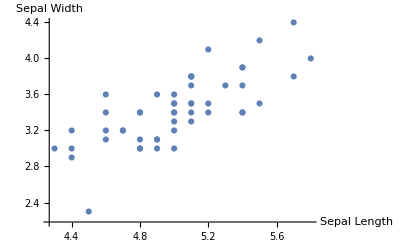

```mathematica
ListPlot[setosaSamples[[All, {1,2}]], AxesLabel->{"Sepal Length", "Sepal Width"}]
```

```mathematica
samplesByClass=GroupBy[irisData,Last];
```

```mathematica
classLabels = Keys[samplesByClass]
```

{setosa,versicolor,virginica}

```mathematica
featuresandclasses[i_, j_]:= GroupBy[irisData, Last]
```

<|setosa→{{5.1,3.5,1.4,0.2,setosa},{4.9,3.,1.4,0.2,setosa},{4.7,3.2,1.3,0.2,setosa},{4.6,3.1,1.5,0.2,setosa},{5.,3.6,1.4,0.2,setosa},{5.4,3.9,1.7,0.4,setosa},{4.6,3.4,1.4,0.3,setosa},{5.,3.4,1.5,0.2,setosa},{4.4,2.9,1.4,0.2,setosa},{4.9,3.1,1.5,0.1,setosa},{5.4,3.7,1.5,0.2,setosa},{4.8,3.4,1.6,0.2,setosa},{4.8,3.,1.4,0.1,setosa},{4.3,3.,1.1,0.1,setosa},{5.8,4.,1.2,0.2,setosa},{5.7,4.4,1.5,0.4,setosa},{5.4,3.9,1.3,0.4,setosa},{5.1,3.5,1.4,0.3,setosa},{5.7,3.8,1.7,0.3,setosa},{5.1,3.8,1.5,0.3,setosa},{5.4,3.4,1.7,0.2,setosa},{5.1,3.7,1.5,0.4,setosa},{4.6,3.6,1.,0.2,setosa},{5.1,3.3,1.7,0.5,setosa},{4.8,3.4,1.9,0.2,setosa},{5.,3.,1.6,0.2,setosa},{5.,3.4,1.6,0.4,setosa},{5.2,3.5,1.5,0.2,setosa},{5.2,3.4,1.4,0.2,setosa},{4.7,3.2,1.6,0.2,setosa},{4.8,3.1,1.6,0.2,setosa},{5.4,3.4,1.5,0.4,setosa},{5.2,4.1,1.5,0.1,setosa},{5.5,4.2,1.4,0.2,setosa},{4.9,3.1,1.5,0.2,setosa},{5.,3.2,1.2,0.2,setosa},{5.5,3.5,1.3,0.2,setosa},{4.9,3.6,1.4,0.1,setosa},{4.4,3.,1.3,0.2,setosa},{5.1,3.4,1.5,0.2,setosa},{5.,3.5,1.3,0.3,setosa},{4.5,2.3,1.3,0.3,setosa},{4.4,3.2,1.3,0.2,setosa},{5.,3.5,1.6,0.6,setosa},{5.1,3.8,1.9,0.4,setosa},{4.8,3.,1.4,0.3,setosa},{5.1,3.8,1.6,0.2,setosa},{4.6,3.2,1.4,0.2,setosa},{5.3,3.7,1.5,0.2,setosa},{5.,3.3,1.4,0.2,setosa}},versicolor→{{7.,3.2,4.7,1.4,versicolor},{6.4,3.2,4.5,1.5,versicolor},{6.9,3.1,4.9,1.5,versicolor},{5.5,2.3,4.,1.3,versicolor},{6.5,2.8,4.6,1.5,versicolor},{5.7,2.8,4.5,1.3,versicolor},{6.3,3.3,4.7,1.6,versicolor},{4.9,2.4,3.3,1.,versicolor},{6.6,2.9,4.6,1.3,versicolor},{5.2,2.7,3.9,1.4,versicolor},{5.,2.,3.5,1.,versicolor},{5.9,3.,4.2,1.5,versicolor},{6.,2.2,4.,1.,versicolor},{6.1,2.9,4.7,1.4,versicolor},{5.6,2.9,3.6,1.3,versicolor},{6.7,3.1,4.4,1.4,versicolor},{5.6,3.,4.5,1.5,versicolor},{5.8,2.7,4.1,1.,versicolor},{6.2,2.2,4.5,1.5,versicolor},{5.6,2.5,3.9,1.1,versicolor},{5.9,3.2,4.8,1.8,versicolor},{6.1,2.8,4.,1.3,versicolor},{6.3,2.5,4.9,1.5,versicolor},{6.1,2.8,4.7,1.2,versicolor},{6.4,2.9,4.3,1.3,versicolor},{6.6,3.,4.4,1.4,versicolor},{6.8,2.8,4.8,1.4,versicolor},{6.7,3.,5.,1.7,versicolor},{6.,2.9,4.5,1.5,versicolor},{5.7,2.6,3.5,1.,versicolor},{5.5,2.4,3.8,1.1,versicolor},{5.5,2.4,3.7,1.,versicolor},{5.8,2.7,3.9,1.2,versicolor},{6.,2.7,5.1,1.6,versicolor},{5.4,3.,4.5,1.5,versicolor},{6.,3.4,4.5,1.6,versicolor},{6.7,3.1,4.7,1.5,versicolor},{6.3,2.3,4.4,1.3,versicolor},{5.6,3.,4.1,1.3,versicolor},{5.5,2.5,4.,1.3,versicolor},{5.5,2.6,4.4,1.2,versicolor},{6.1,3.,4.6,1.4,versicolor},{5.8,2.6,4.,1.2,versicolor},{5.,2.3,3.3,1.,versicolor},{5.6,2.7,4.2,1.3,versicolor},{5.7,3.,4.2,1.2,versicolor},{5.7,2.9,4.2,1.3,versicolor},{6.2,2.9,4.3,1.3,versicolor},{5.1,2.5,3.,1.1,versicolor},{5.7,2.8,4.1,1.3,versicolor}},virginica→{{6.3,3.3,6.,2.5,virginica},{5.8,2.7,5.1,1.9,virginica},{7.1,3.,5.9,2.1,virginica},{6.3,2.9,5.6,1.8,virginica},{6.5,3.,5.8,2.2,virginica},{7.6,3.,6.6,2.1,virginica},{4.9,2.5,4.5,1.7,virginica},{7.3,2.9,6.3,1.8,virginica},{6.7,2.5,5.8,1.8,virginica},{7.2,3.6,6.1,2.5,virginica},{6.5,3.2,5.1,2.,virginica},{6.4,2.7,5.3,1.9,virginica},{6.8,3.,5.5,2.1,virginica},{5.7,2.5,5.,2.,virginica},{5.8,2.8,5.1,2.4,virginica},{6.4,3.2,5.3,2.3,virginica},{6.5,3.,5.5,1.8,virginica},{7.7,3.8,6.7,2.2,virginica},{7.7,2.6,6.9,2.3,virginica},{6.,2.2,5.,1.5,virginica},{6.9,3.2,5.7,2.3,virginica},{5.6,2.8,4.9,2.,virginica},{7.7,2.8,6.7,2.,virginica},{6.3,2.7,4.9,1.8,virginica},{6.7,3.3,5.7,2.1,virginica},{7.2,3.2,6.,1.8,virginica},{6.2,2.8,4.8,1.8,virginica},{6.1,3.,4.9,1.8,virginica},{6.4,2.8,5.6,2.1,virginica},{7.2,3.,5.8,1.6,virginica},{7.4,2.8,6.1,1.9,virginica},{7.9,3.8,6.4,2.,virginica},{6.4,2.8,5.6,2.2,virginica},{6.3,2.8,5.1,1.5,virginica},{6.1,2.6,5.6,1.4,virginica},{7.7,3.,6.1,2.3,virginica},{6.3,3.4,5.6,2.4,virginica},{6.4,3.1,5.5,1.8,virginica},{6.,3.,4.8,1.8,virginica},{6.9,3.1,5.4,2.1,virginica},{6.7,3.1,5.6,2.4,virginica},{6.9,3.1,5.1,2.3,virginica},{5.8,2.7,5.1,1.9,virginica},{6.8,3.2,5.9,2.3,virginica},{6.7,3.3,5.7,2.5,virginica},{6.7,3.,5.2,2.3,virginica},{6.3,2.5,5.,1.9,virginica},{6.5,3.,5.2,2.,virginica},{6.2,3.4,5.4,2.3,virginica},{5.9,3.,5.1,1.8,virginica}}|>

ListPlot::lpn: featuresandclasses is not a list of numbers or pairs of numbers.